```mathematica
SetDirectory@NotebookDirectory[];
QuantizeBits[x_,bits_,dither_:0]:=Clip[Round[x*(Power[2,bits]-1)+dither]/(Power[2,bits]-1)]
remaptri[v_]=Piecewise[{{√(2v)-1, v≤1/2}, {1-√(2-2v), v>1/2}}];
```

```mathematica
SampleArrayWithWrap[arr_,x_,y_]:=Module[{dims=Dimensions[arr]},arr[[Mod[x,dims[[1]],1],Mod[y,dims[[2]],1]]]]
origSignal = Table[x/128,{y,0,127},{x,0,127}];
ArrayPlot[origSignal,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ArrayPlot[QuantizeBits[#1,3]&/@origSignal,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ditheredWhite=Map[QuantizeBits[#1,3,RandomReal[]-0.5]&,origSignal,{2}];
ArrayPlot[ditheredWhite,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ArrayPlot[Map[QuantizeBits[#1,3,(RandomReal[]-0.5)*2]&,origSignal,{2}],ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ArrayPlot[Map[QuantizeBits[#1,3,(RandomReal[]+RandomReal[]-1)]&,origSignal,{2}],ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
Bayer[x_,y_,level_]:=Mod[Mod[BitShiftRight[x,level],2]+1+2*Mod[BitShiftRight[y,level],2],4]+If[level==0,0,4*Bayer[x,y,level-1]]
bayer3=Table[Bayer[x,y,2],{y,0,7},{x,0,7}]/63;
bayer6=Table[Bayer[x,y,5],{y,0,63},{x,0,63}]/(64*64-1);
```

```mathematica
ditheredBayer=MapIndexed[QuantizeBits[#1,3,SampleArrayWithWrap[bayer3,#2[[1]],#2[[2]]]-0.5]&,origSignal,{2}];
```

```mathematica
ArrayPlot[bayer3,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ArrayPlot[ditheredBayer,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
InterleavedGradientNoise[x_,y_]:=FractionalPart[52.9829189*FractionalPart[0.06711056*x+0.00583715*y]]
```

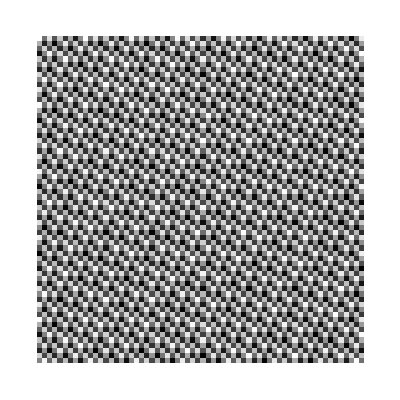

```mathematica
ArrayPlot[Table[InterleavedGradientNoise[x,y],{y,0,63},{x,0,63}]]
```

```mathematica
ditheredInterleaved=MapIndexed[QuantizeBits[#1,3,InterleavedGradientNoise[#2[[1]],#2[[2]]]-0.5]&,origSignal,{2}];
ArrayPlot[ditheredInterleaved,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
blueNoise64={{0.49169922,0.17871094,0.34204102,0.85205078,0.50048828,0.11206055,0.87304688,0.21777344,0.62182617,0.34716797,0.84228516,0.57080078,0.38940430,0.28613281,0.98217773,0.83251953,0.29345703,0.19848633,0.98510742,0.80273438,0.58886719,0.16503906,0.60424805,0.75878906,0.34350586,0.60229492,0.84887695,0.23486328,0.83374023,0.10961914,0.91674805,0.59643555,0.19604492,0.46630859,0.87548828,0.67041016,0.16162109,0.04003906,0.33374023,0.87329102,0.64575195,0.28906250,0.45703125,0.65039062,0.29052734,0.79638672,0.59887695,0.38305664,0.10815430,0.62988281,0.85839844,0.20166016,0.12915039,0.60888672,0.24218750,0.11279297,0.67480469,0.57006836,0.91186523,0.19750977,0.51220703,0.83740234,0.02636719,0.44433594},{0.94311523,0.57739258,0.77758789,0.21264648,0.99267578,0.66967773,0.40283203,0.00683594,0.67553711,0.10205078,0.45336914,0.95996094,0.51123047,0.85791016,0.07348633,0.56298828,0.15893555,0.53295898,0.44946289,0.34399414,0.94580078,0.01293945,0.77490234,0.99755859,0.10400391,0.47949219,0.77734375,0.03686523,0.46655273,0.69580078,0.34960938,0.80908203,0.62109375,0.05639648,0.52099609,0.22314453,0.98120117,0.41064453,0.66674805,0.11059570,0.93237305,0.38183594,0.00268555,0.80322266,0.60815430,0.24072266,0.97265625,0.02343750,0.84057617,0.35620117,0.99707031,0.49951172,0.71557617,0.02270508,0.46582031,0.96704102,0.79003906,0.01977539,0.37304688,0.11303711,0.30468750,0.10424805,0.98242188,0.23828125},{0.75659180,0.06201172,0.53271484,0.62817383,0.36987305,0.29003906,0.57592773,0.24975586,0.82739258,0.29809570,0.70849609,0.17578125,0.59814453,0.70117188,0.39990234,0.09082031,0.67163086,0.05761719,0.91528320,0.22094727,0.61523438,0.38574219,0.49072266,0.43237305,0.26000977,0.62646484,0.33203125,0.92797852,0.64257812,0.31176758,0.97827148,0.16918945,0.41015625,0.93334961,0.27221680,0.71801758,0.81030273,0.76440430,0.23925781,0.49121094,0.64062500,0.18261719,0.53125000,0.12670898,0.97802734,0.46264648,0.19702148,0.67456055,0.44482422,0.18896484,0.27416992,0.81787109,0.57568359,0.30297852,0.79418945,0.26245117,0.46679688,0.28515625,0.76684570,0.96411133,0.61669922,0.38256836,0.63159180,0.38818359},{0.88745117,0.32763672,0.18041992,0.84790039,0.93481445,0.11791992,0.95678711,0.77343750,0.45117188,0.97021484,0.86450195,0.00537109,0.37231445,0.98681641,0.22607422,0.76391602,0.44775391,0.83691406,0.32153320,0.69604492,0.10449219,0.85229492,0.72265625,0.16113281,0.04736328,0.94775391,0.74096680,0.12573242,0.18481445,0.85131836,0.47534180,0.30273438,0.00561523,0.63574219,0.89282227,0.43188477,0.26464844,0.51660156,0.04150391,0.33276367,0.81103516,0.88452148,0.65478516,0.42187500,0.32006836,0.03466797,0.55322266,0.77075195,0.42626953,0.09545898,0.71215820,0.36523438,0.93945312,0.18457031,0.53393555,0.68066406,0.90844727,0.16821289,0.50122070,0.69116211,0.42797852,0.79321289,0.82934570,0.06665039},{0.47656250,0.40063477,0.64746094,0.08007812,0.46142578,0.68432617,0.21313477,0.07324219,0.52441406,0.12329102,0.48999023,0.26098633,0.32055664,0.58496094,0.85375977,0.53515625,0.37597656,0.08349609,0.73974609,0.52612305,0.07910156,0.81469727,0.22412109,0.66308594,0.55615234,0.85668945,0.45263672,0.36352539,0.76538086,0.55200195,0.11962891,0.73071289,0.74755859,0.48120117,0.07714844,0.58325195,0.07861328,0.79785156,0.87377930,0.70532227,0.40869141,0.04711914,0.21728516,0.80175781,0.74609375,0.98266602,0.84033203,0.36059570,0.93432617,0.82055664,0.59838867,0.07690430,0.49780273,0.10302734,0.62011719,0.37500000,0.20336914,0.59008789,0.89453125,0.23168945,0.09863281,0.29223633,0.13989258,0.65234375},{0.25048828,0.78784180,0.14526367,0.82910156,0.51879883,0.26831055,0.70947266,0.64526367,0.34082031,0.76269531,0.65136719,0.89501953,0.79492188,0.06274414,0.17749023,0.81225586,0.31713867,0.49804688,0.88891602,0.65356445,0.28857422,0.49096680,0.98950195,0.36645508,0.21435547,0.51342773,0.09619141,0.39868164,0.95825195,0.02685547,0.23974609,0.91284180,0.33618164,0.15600586,0.86132812,0.25488281,0.92480469,0.59252930,0.30517578,0.51367188,0.96899414,0.34643555,0.66186523,0.48852539,0.37744141,0.13452148,0.63525391,0.07885742,0.66455078,0.00805664,0.29638672,0.39794922,0.85644531,0.72143555,0.95458984,0.02978516,0.76416016,0.06835938,0.34033203,0.55517578,0.94970703,0.49340820,0.76025391,0.97045898},{0.55859375,0.94458008,0.36083984,0.19189453,0.60131836,0.02709961,0.89331055,0.39575195,0.93115234,0.19799805,0.57910156,0.11132812,0.40039062,0.64086914,0.67333984,0.03955078,0.89013672,0.25659180,0.05908203,0.95922852,0.27270508,0.41381836,0.88818359,0.61425781,0.84448242,0.13647461,0.68579102,0.75366211,0.26269531,0.81713867,0.45166016,0.82958984,0.56176758,0.65942383,0.39257812,0.73754883,0.37377930,0.19433594,0.80200195,0.00634766,0.27709961,0.18847656,0.78955078,0.96215820,0.01049805,0.24096680,0.44262695,0.22265625,0.47241211,0.61621094,0.90966797,0.22485352,0.05297852,0.30639648,0.54272461,0.82202148,0.42163086,0.93872070,0.62597656,0.03808594,0.74902344,0.37475586,0.58642578,0.01855469},{0.75561523,0.79589844,0.66918945,0.89111328,0.26147461,0.81152344,0.53637695,0.15551758,0.49731445,0.00927734,0.37573242,0.99658203,0.29736328,0.23022461,0.38623047,0.21093750,0.59594727,0.82788086,0.52661133,0.19116211,0.70751953,0.33007812,0.10375977,0.73046875,0.47021484,0.92724609,0.28491211,0.89038086,0.59082031,0.65600586,0.07470703,0.20825195,0.45654297,0.99145508,0.12792969,0.01220703,0.61010742,0.97851562,0.42700195,0.65722656,0.53344727,0.89257812,0.09765625,0.35009766,0.53100586,0.60083008,0.78515625,0.93261719,0.26049805,0.73632812,0.42675781,0.58471680,0.79223633,0.24023438,0.67602539,0.33520508,0.17041016,0.79711914,0.25439453,0.52075195,0.13500977,0.28686523,0.82275391,0.31469727},{0.21337891,0.09326172,0.51733398,0.07080078,0.38037109,0.61840820,0.21533203,0.94238281,0.67529297,0.73461914,0.12719727,0.75830078,0.57641602,0.83789062,0.88305664,0.48706055,0.70336914,0.35229492,0.71997070,0.14160156,0.82495117,0.93041992,0.49560547,0.02514648,0.21606445,0.64550781,0.43090820,0.11645508,0.39916992,0.19384766,0.92163086,0.71923828,0.38232422,0.88208008,0.50781250,0.26123047,0.56738281,0.15380859,0.78393555,0.11376953,0.40429688,0.72387695,0.16772461,0.70971680,0.43920898,0.98046875,0.86718750,0.32568359,0.03002930,0.84960938,0.17065430,0.97534180,0.05029297,0.40625000,0.87988281,0.50927734,0.02075195,0.36914062,0.70727539,0.43017578,0.90771484,0.63940430,0.06225586,0.87182617},{0.32373047,0.26879883,0.61767578,0.75292969,0.97900391,0.34155273,0.08911133,0.78442383,0.25805664,0.85498047,0.50097656,0.40673828,0.61206055,0.02294922,0.16943359,0.35913086,0.11328125,0.98803711,0.26074219,0.45043945,0.61791992,0.19677734,0.36694336,0.73779297,0.98144531,0.37060547,0.04516602,0.79980469,0.24877930,0.79443359,0.56372070,0.13598633,0.66894531,0.37939453,0.69262695,0.10107422,0.80541992,0.91015625,0.30981445,0.95263672,0.30346680,0.58715820,0.85766602,0.01684570,0.33081055,0.73095703,0.10693359,0.62670898,0.54296875,0.19555664,0.39135742,0.46899414,0.71386719,0.57495117,0.19335938,0.97460938,0.60644531,0.63745117,0.97656250,0.14208984,0.36718750,0.77026367,0.97070312,0.46752930},{0.70800781,0.01562500,0.40576172,0.80761719,0.26855469,0.71655273,0.43066406,0.46923828,0.57104492,0.39770508,0.96777344,0.08447266,0.21948242,0.76635742,0.92700195,0.54736328,0.82421875,0.62133789,0.04223633,0.53808594,0.99536133,0.00659180,0.81616211,0.31152344,0.55346680,0.83471680,0.49609375,0.63427734,0.99780273,0.46166992,0.35400391,0.88012695,0.23876953,0.02465820,0.94018555,0.74877930,0.26513672,0.42065430,0.58935547,0.65698242,0.02807617,0.82446289,0.45605469,0.38281250,0.55957031,0.23193359,0.41992188,0.82006836,0.41625977,0.94189453,0.69067383,0.63037109,0.28710938,0.45581055,0.74804688,0.07592773,0.48291016,0.88696289,0.03857422,0.32031250,0.60986328,0.04833984,0.18359375,0.51318359},{0.85815430,0.54638672,0.91650391,0.20385742,0.62451172,0.02001953,0.93847656,0.73803711,0.02758789,0.17895508,0.33544922,0.56787109,0.27197266,0.68627930,0.11181641,0.46386719,0.24389648,0.75317383,0.56762695,0.29077148,0.81054688,0.11596680,0.49267578,0.88110352,0.23510742,0.14453125,0.01025391,0.91552734,0.21899414,0.09472656,0.69775391,0.11694336,0.49438477,0.62255859,0.20068359,0.60766602,0.49414062,0.00512695,0.82861328,0.17309570,0.37817383,0.24194336,0.17651367,0.78198242,0.14794922,0.99829102,0.17700195,0.75195312,0.05419922,0.42846680,0.26171875,0.90258789,0.10766602,0.82812500,0.15112305,0.56591797,0.26904297,0.16967773,0.78588867,0.49365234,0.81518555,0.41333008,0.66601562,0.91918945},{0.27929688,0.75390625,0.09350586,0.51000977,0.47363281,0.15234375,0.40551758,0.28002930,0.81982422,0.90478516,0.71533203,0.85888672,0.36572266,0.80078125,0.50244141,0.90673828,0.38110352,0.01367188,0.18505859,0.68603516,0.47998047,0.42773438,0.15722656,0.63305664,0.74389648,0.44091797,0.73535156,0.35424805,0.64355469,0.53784180,0.89746094,0.41088867,0.74340820,0.17163086,0.93994141,0.42138672,0.28125000,0.13232422,0.67236328,0.92749023,0.50463867,0.57666016,0.89648438,0.95141602,0.69458008,0.35693359,0.59790039,0.25024414,0.93090820,0.79028320,0.20605469,0.00170898,0.65405273,0.25170898,0.95654297,0.68872070,0.86083984,0.34619141,0.10522461,0.69677734,0.23046875,0.97338867,0.31518555,0.12548828},{0.44677734,0.59106445,0.73217773,0.26196289,0.86767578,0.97998047,0.67504883,0.37182617,0.07739258,0.58447266,0.57983398,0.14697266,0.50317383,0.18774414,0.02880859,0.62744141,0.40478516,0.81347656,0.19775391,0.93896484,0.04614258,0.60449219,0.96093750,0.19018555,0.51782227,0.96752930,0.32177734,0.25903320,0.85400391,0.15283203,0.58691406,0.32299805,0.03540039,0.79052734,0.22924805,0.59545898,0.88549805,0.30395508,0.71411133,0.22290039,0.06640625,0.77050781,0.62207031,0.10888672,0.48144531,0.65209961,0.83813477,0.07299805,0.49023438,0.62158203,0.38696289,0.52929688,0.52563477,0.78369141,0.34887695,0.41040039,0.01074219,0.54809570,0.66821289,0.36791992,0.43310547,0.89965820,0.50439453,0.03149414},{0.94287109,0.17114258,0.00854492,0.41845703,0.73291016,0.55981445,0.75634766,0.51147461,0.96508789,0.20214844,0.79345703,0.03442383,0.85693359,0.94067383,0.76953125,0.26611328,0.75024414,0.97387695,0.56665039,0.38598633,0.74267578,0.29125977,0.67871094,0.37011719,0.07666016,0.86279297,0.60717773,0.11401367,0.49218750,0.75683594,0.06884766,0.92626953,0.45874023,0.68945312,0.38134766,0.75146484,0.47314453,0.93725586,0.59521484,0.43164062,0.85620117,0.27734375,0.48583984,0.00341797,0.36303711,0.21582031,0.94628906,0.67822266,0.25317383,0.92602539,0.64892578,0.79467773,0.05346680,0.96435547,0.16577148,0.58300781,0.84741211,0.29443359,0.92944336,0.17626953,0.13183594,0.75585938,0.20947266,0.68188477},{0.33032227,0.70410156,0.83642578,0.20361328,0.39013672,0.33911133,0.08886719,0.16992188,0.43823242,0.53686523,0.25854492,0.29980469,0.41894531,0.69409180,0.46704102,0.07226562,0.47900391,0.09277344,0.65917969,0.26293945,0.10473633,0.84912109,0.93579102,0.33178711,0.73510742,0.35156250,0.04394531,0.70434570,0.99877930,0.42260742,0.63598633,0.24755859,0.56542969,0.89868164,0.15014648,0.83959961,0.17602539,0.00830078,0.36254883,0.71948242,0.30419922,0.08422852,0.70605469,0.30664062,0.85253906,0.05664062,0.47094727,0.31884766,0.75927734,0.02221680,0.35278320,0.13159180,0.27832031,0.53149414,0.21118164,0.80810547,0.46728516,0.66528320,0.98559570,0.71093750,0.42333984,0.61401367,0.36816406,0.83398438},{0.11547852,0.52490234,0.31738281,0.89941406,0.04785156,0.71044922,0.24536133,0.98315430,0.88769531,0.64697266,0.10839844,0.92211914,0.63476562,0.14038086,0.26220703,0.34838867,0.86059570,0.43408203,0.99316406,0.35937500,0.50292969,0.13110352,0.53002930,0.02856445,0.15844727,0.61645508,0.65771484,0.22753906,0.50268555,0.23364258,0.80053711,0.95068359,0.18115234,0.33813477,0.45190430,0.06933594,0.57763672,0.32397461,0.11108398,0.86596680,0.63232422,0.96679688,0.91601562,0.62719727,0.36108398,0.78686523,0.54956055,0.84106445,0.09887695,0.48974609,0.98657227,0.71850586,0.77197266,0.45678711,0.89355469,0.02099609,0.14843750,0.29199219,0.54760742,0.00195312,0.31079102,0.52905273,0.06103516,0.57373047},{0.92407227,0.66210938,0.13378906,0.51757812,0.92138672,0.60473633,0.43286133,0.66479492,0.31298828,0.39282227,0.77172852,0.58569336,0.23144531,0.98999023,0.56445312,0.68896484,0.81274414,0.16552734,0.65258789,0.89697266,0.74194336,0.42919922,0.77465820,0.89379883,0.40185547,0.83105469,0.37646484,0.88378906,0.71704102,0.09228516,0.46606445,0.33422852,0.03833008,0.62377930,0.76049805,0.90869141,0.79956055,0.51708984,0.77416992,0.17724609,0.56005859,0.17333984,0.52832031,0.13256836,0.22534180,0.92993164,0.40893555,0.26977539,0.67993164,0.58740234,0.11743164,0.26342773,0.64428711,0.89794922,0.40698242,0.61352539,0.72338867,0.44067383,0.09399414,0.80688477,0.16894531,0.94677734,0.84570312,0.34448242},{0.24853516,0.00292969,0.46459961,0.74829102,0.30834961,0.78857422,0.02661133,0.53759766,0.88793945,0.19409180,0.08105469,0.88916016,0.34252930,0.78710938,0.00317383,0.37963867,0.08129883,0.22778320,0.31274414,0.04638672,0.62622070,0.20678711,0.37768555,0.97753906,0.29370117,0.53369141,0.05541992,0.93920898,0.18090820,0.58422852,0.95776367,0.65087891,0.86914062,0.27392578,0.67749023,0.14501953,0.22729492,0.99926758,0.68334961,0.32910156,0.42944336,0.26391602,0.82519531,0.44506836,0.68530273,0.11889648,0.64135742,0.09179688,0.96166992,0.82836914,0.43432617,0.40307617,0.68408203,0.15307617,0.07373047,0.22143555,0.88061523,0.19238281,0.97216797,0.58959961,0.66796875,0.26806641,0.08789062,0.76367188},{0.47387695,0.81591797,0.94262695,0.23461914,0.40722656,0.97314453,0.15356445,0.64404297,0.05126953,0.67895508,0.49853516,0.40380859,0.03076172,0.71484375,0.52124023,0.86181641,0.48315430,0.60327148,0.70166016,0.13525391,0.79931641,0.92529297,0.53076172,0.65429688,0.06811523,0.76513672,0.26538086,0.50195312,0.76489258,0.37426758,0.10913086,0.53198242,0.30224609,0.93408203,0.45068359,0.01513672,0.57397461,0.40112305,0.12646484,0.96557617,0.05273438,0.86572266,0.59960938,0.00610352,0.77221680,0.32983398,0.87475586,0.75268555,0.38867188,0.18066406,0.67773438,0.04589844,0.92871094,0.27539062,0.77001953,0.46215820,0.73876953,0.63281250,0.36962891,0.84472656,0.48828125,0.38476562,0.71826172,0.54125977},{0.63867188,0.16699219,0.56518555,0.04443359,0.76196289,0.28247070,0.59936523,0.24365234,0.37109375,0.80029297,0.97631836,0.50756836,0.27343750,0.63842773,0.26489258,0.09692383,0.95092773,0.55053711,0.86157227,0.39184570,0.60278320,0.23779297,0.13818359,0.19091797,0.85424805,0.65844727,0.16040039,0.70214844,0.40234375,0.88989258,0.25146484,0.77807617,0.03222656,0.53540039,0.72583008,0.35766602,0.21972656,0.86791992,0.74243164,0.63452148,0.24511719,0.43261719,0.77441406,0.15625000,0.52197266,0.97143555,0.38061523,0.56835938,0.63818359,0.87426758,0.23803711,0.75756836,0.48388672,0.33398438,0.90820312,0.53955078,0.02954102,0.17456055,0.24682617,0.42871094,0.04125977,0.76245117,0.34472656,0.14428711},{0.84936523,0.32861328,0.46362305,0.61157227,0.89404297,0.45922852,0.83984375,0.98901367,0.14379883,0.76293945,0.30151367,0.17504883,0.94897461,0.88427734,0.57226562,0.24487305,0.39477539,0.87280273,0.15209961,0.27246094,0.95361328,0.46313477,0.73486328,0.00146484,0.29565430,0.51196289,0.97973633,0.64038086,0.03930664,0.17382812,0.66381836,0.93359375,0.60913086,0.16723633,0.78979492,0.30883789,0.73144531,0.08837891,0.52539062,0.37402344,0.93139648,0.53173828,0.89428711,0.31127930,0.73266602,0.03344727,0.20019531,0.04370117,0.50415039,0.18554688,0.01416016,0.98388672,0.61694336,0.53564453,0.23706055,0.81372070,0.39672852,0.99609375,0.68212891,0.88281250,0.12011719,0.93774414,0.59985352,0.93066406},{0.75708008,0.14233398,0.41455078,0.85083008,0.14672852,0.10644531,0.54589844,0.40844727,0.90600586,0.58544922,0.68310547,0.71630859,0.07153320,0.41210938,0.73925781,0.09375000,0.64453125,0.01953125,0.72436523,0.43750000,0.21484375,0.73730469,0.38720703,0.58618164,0.87744141,0.32885742,0.84497070,0.25830078,0.85156250,0.43994141,0.75000000,0.32324219,0.46044922,0.24462891,0.85058594,0.43457031,0.99951172,0.13940430,0.80517578,0.03173828,0.41406250,0.07836914,0.23266602,0.65747070,0.40991211,0.57934570,0.24047852,0.95410156,0.74658203,0.79394531,0.44750977,0.37207031,0.16308594,0.70141602,0.08715820,0.22363281,0.59375000,0.87817383,0.08935547,0.55493164,0.50976562,0.30566406,0.27490234,0.04541016},{0.96948242,0.35327148,0.68457031,0.28222656,0.52880859,0.22656250,0.64306641,0.01098633,0.48876953,0.07177734,0.21826172,0.37719727,0.91577148,0.44311523,0.81933594,0.29321289,0.97485352,0.31640625,0.50878906,0.83178711,0.92236328,0.59692383,0.07006836,0.94384766,0.52783203,0.06958008,0.58178711,0.15429688,0.48413086,0.58984375,0.08569336,0.38525391,0.95581055,0.13476562,0.55444336,0.66162109,0.20581055,0.61987305,0.28271484,0.77832031,0.58276367,0.70898438,0.10229492,0.91821289,0.77929688,0.32470703,0.62353516,0.86352539,0.34228516,0.61572266,0.06347656,0.82983398,0.52734375,0.71606445,0.88476562,0.48950195,0.69287109,0.29028320,0.74438477,0.17187500,0.79174805,0.70288086,0.48168945,0.53710938},{0.61108398,0.03100586,0.89672852,0.06713867,0.98706055,0.76977539,0.72094727,0.33886719,0.25976562,0.74682617,0.89990234,0.44653320,0.25292969,0.68505859,0.14282227,0.50073242,0.68090820,0.80981445,0.07104492,0.47851562,0.00976562,0.27563477,0.41772461,0.20996094,0.80712891,0.74853516,0.34521484,0.96875000,0.87792969,0.35131836,0.94555664,0.22583008,0.68017578,0.91064453,0.03588867,0.81250000,0.45458984,0.55468750,0.40087891,0.99682617,0.28369141,0.46948242,0.83837891,0.43554688,0.07275391,0.93652344,0.09985352,0.43139648,0.25122070,0.74926758,0.50390625,0.29614258,0.12622070,0.33691406,0.03979492,0.93750000,0.33325195,0.03784180,0.59301758,0.21801758,0.35986328,0.94824219,0.09814453,0.17797852},{0.30029297,0.56884766,0.43676758,0.54223633,0.19580078,0.37915039,0.83715820,0.25097656,0.92651367,0.56030273,0.08764648,0.80737305,0.98095703,0.57055664,0.02539062,0.79882812,0.33666992,0.60742188,0.39355469,0.72949219,0.18334961,0.68701172,0.90991211,0.54443359,0.16088867,0.12158203,0.56347656,0.18994141,0.70361328,0.02416992,0.76831055,0.56127930,0.05566406,0.62329102,0.30712891,0.14575195,0.25390625,0.84643555,0.68798828,0.87451172,0.20727539,0.69726562,0.15063477,0.56689453,0.30053711,0.20703125,0.79150391,0.48779297,0.04687500,0.15747070,0.98608398,0.61035156,0.91455078,0.64648438,0.71362305,0.17089844,0.90917969,0.56274414,0.76782227,0.96313477,0.24340820,0.62524414,0.48486328,0.78881836},{0.71459961,0.93286133,0.21850586,0.83032227,0.10742188,0.85937500,0.57177734,0.45141602,0.15454102,0.47460938,0.65283203,0.32348633,0.11914062,0.71508789,0.51440430,0.20263672,0.97290039,0.15136719,0.09741211,0.86889648,0.54687500,0.33959961,0.78833008,0.30737305,0.87719727,0.64770508,0.91381836,0.45849609,0.24169922,0.41552734,0.63916016,0.38159180,0.34326172,0.84545898,0.47338867,0.78027344,0.01879883,0.34423828,0.06762695,0.12890625,0.49829102,0.00439453,0.73168945,0.47119141,0.84082031,0.62963867,0.37036133,0.93603516,0.66650391,0.35791016,0.79296875,0.37866211,0.85961914,0.25561523,0.48339844,0.37695312,0.64794922,0.19653320,0.48193359,0.03759766,0.70312500,0.88671875,0.01269531,0.24121094},{0.55664062,0.11474609,0.42553711,0.69091797,0.70483398,0.03564453,0.36840820,0.11621094,0.72558594,0.94946289,0.12841797,0.54174805,0.23315430,0.80493164,0.35644531,0.89599609,0.46997070,0.75122070,0.29174805,0.80346680,0.23730469,0.96337891,0.42968750,0.66943359,0.00024414,0.45947266,0.31689453,0.69824219,0.12817383,0.77319336,0.89477539,0.11450195,0.22509766,0.01538086,0.73608398,0.95898438,0.34277344,0.65625000,0.44189453,0.82397461,0.90234375,0.33447266,0.61499023,0.95117188,0.02197266,0.57348633,0.18798828,0.71142578,0.24414062,0.87084961,0.51416016,0.05859375,0.28173828,0.01000977,0.59033203,0.10595703,0.84692383,0.77246094,0.39843750,0.85034180,0.32226562,0.58251953,0.37133789,0.95288086},{0.32836914,0.77685547,0.01928711,0.90576172,0.27514648,0.46484375,0.90698242,0.67846680,0.84619141,0.59179688,0.28784180,0.83154297,0.94433594,0.45483398,0.06030273,0.58789062,0.23608398,0.06567383,0.62915039,0.35742188,0.58666992,0.11669922,0.16650391,0.35058594,0.52319336,0.14550781,0.82177734,0.59448242,0.99511719,0.30908203,0.43896484,0.58813477,0.76123047,0.93164062,0.58398438,0.50537109,0.19213867,0.83862305,0.55590820,0.15405273,0.27978516,0.41528320,0.92773438,0.21508789,0.70092773,0.89819336,0.46826172,0.07250977,0.40356445,0.75219727,0.31054688,0.63964844,0.56982422,0.70556641,0.91699219,0.13842773,0.27465820,0.63403320,0.11572266,0.52978516,0.27758789,0.81176758,0.49658203,0.90747070},{0.04296875,0.38012695,0.62231445,0.16601562,0.64843750,0.19726562,0.48217773,0.22631836,0.29760742,0.01342773,0.44702148,0.39111328,0.14306641,0.68725586,0.18408203,0.63549805,0.92578125,0.50219727,0.40600586,0.96728516,0.06982422,0.73852539,0.65112305,0.96289062,0.78491211,0.20898438,0.05834961,0.41967773,0.75341797,0.06787109,0.85864258,0.68750000,0.43603516,0.39233398,0.13354492,0.31958008,0.74707031,0.01757812,0.92553711,0.76171875,0.52026367,0.05224609,0.72631836,0.16845703,0.32617188,0.11425781,0.33154297,0.80297852,0.18969727,0.96264648,0.25927734,0.80615234,0.03198242,0.44140625,0.80834961,0.32543945,0.99096680,0.43627930,0.27783203,0.95019531,0.04760742,0.42211914,0.10131836,0.66992188},{0.21191406,0.46850586,0.98339844,0.49047852,0.57153320,0.14965820,0.84326172,0.99487305,0.59667969,0.16455078,0.80004883,0.98168945,0.65966797,0.35473633,0.97094727,0.29516602,0.14135742,0.75048828,0.84301758,0.55395508,0.45996094,0.21630859,0.90527344,0.33789062,0.41479492,0.94506836,0.69946289,0.23852539,0.64477539,0.15258789,0.31201172,0.02929688,0.64965820,0.25683594,0.05615234,0.86938477,0.51025391,0.14477539,0.36450195,0.21997070,0.64868164,0.45434570,0.29541016,0.62500000,0.54858398,0.45092773,0.68481445,0.97192383,0.66259766,0.51977539,0.09033203,0.39624023,0.93188477,0.33764648,0.71337891,0.05517578,0.54418945,0.76098633,0.12475586,0.81811523,0.61962891,0.18823242,0.72119141,0.82666016},{0.94726562,0.39892578,0.73022461,0.05175781,0.81860352,0.68676758,0.54785156,0.08959961,0.73388672,0.35546875,0.51953125,0.11230469,0.01733398,0.48535156,0.86962891,0.51562500,0.04467773,0.70458984,0.12988281,0.03637695,0.27319336,0.83593750,0.53491211,0.02026367,0.64208984,0.18432617,0.86425781,0.57788086,0.38452148,0.95629883,0.50561523,0.82324219,0.95190430,0.45556641,0.80859375,0.70776367,0.37988281,0.65185547,0.97509766,0.55078125,0.81542969,0.24658203,0.94848633,0.85449219,0.06469727,0.91259766,0.52148438,0.01440430,0.26660156,0.41308594,0.57519531,0.67138672,0.14404297,0.25219727,0.63208008,0.44970703,0.92309570,0.31445312,0.72509766,0.37084961,0.90307617,0.52587891,0.24609375,0.53881836},{0.15649414,0.54833984,0.35595703,0.90722656,0.29467773,0.05932617,0.38549805,0.25415039,0.92114258,0.88232422,0.41137695,0.25781250,0.57324219,0.72216797,0.31250000,0.76904297,0.47265625,0.28930664,0.95239258,0.36157227,0.67114258,0.77954102,0.07568359,0.24145508,0.87890625,0.33227539,0.51855469,0.01147461,0.43872070,0.77539062,0.21240234,0.61083984,0.37451172,0.16137695,0.55737305,0.20312500,0.93823242,0.56640625,0.10571289,0.72241211,0.06005859,0.13696289,0.42456055,0.54052734,0.75952148,0.22998047,0.56396484,0.31909180,0.83447266,0.05371094,0.88574219,0.37524414,0.91967773,0.84179688,0.49389648,0.16430664,0.86621094,0.12109375,0.43701172,0.53662109,0.15502930,0.31420898,0.70043945,0.45898438},{0.02587891,0.69238281,0.12744141,0.76611328,0.43579102,0.96826172,0.56811523,0.12524414,0.44165039,0.04907227,0.60058594,0.76220703,0.91430664,0.20043945,0.10937500,0.62402344,0.36230469,0.59155273,0.16796875,0.87841797,0.51806641,0.14721680,0.55712891,0.37353516,0.63134766,0.75463867,0.20410156,0.84155273,0.30200195,0.57031250,0.86376953,0.19042969,0.57421875,0.90429688,0.03881836,0.71679688,0.40917969,0.29589844,0.57250977,0.90551758,0.32421875,0.60375977,0.94799805,0.08520508,0.36938477,0.20654297,0.89233398,0.12451172,0.75854492,0.49536133,0.25268555,0.13403320,0.72363281,0.03125000,0.09790039,0.68969727,0.26708984,0.50488281,0.02148438,0.68139648,0.96630859,0.82226562,0.11035156,0.79101562},{0.65551758,0.91748047,0.21557617,0.60937500,0.14624023,0.88256836,0.19921875,0.72998047,0.68041992,0.47192383,0.15795898,0.67016602,0.21044922,0.42358398,0.85278320,0.06518555,0.92285156,0.01611328,0.75537109,0.41748047,0.26318359,0.71875000,0.98632812,0.84716797,0.46972656,0.96362305,0.42431641,0.71899414,0.13574219,0.94995117,0.28955078,0.05004883,0.71069336,0.35205078,0.80151367,0.12866211,0.49291992,0.07495117,0.01904297,0.43945312,0.83886719,0.28149414,0.78125000,0.54711914,0.77270508,0.61376953,0.82543945,0.42089844,0.95751953,0.71264648,0.57885742,0.62084961,0.36596680,0.48657227,0.62768555,0.36621094,0.84277344,0.76660156,0.66015625,0.93457031,0.08276367,0.23339844,0.52807617,0.96142578},{0.23999023,0.41430664,0.34814453,0.55639648,0.83666992,0.49755859,0.36328125,0.82617188,0.16259766,0.95483398,0.34936523,0.88598633,0.56469727,0.29418945,0.99902344,0.60961914,0.67211914,0.86816406,0.34545898,0.06127930,0.95703125,0.63720703,0.41918945,0.27856445,0.18725586,0.11083984,0.62841797,0.34985352,0.08642578,0.49926758,0.69750977,0.38891602,0.97607422,0.27954102,0.61865234,0.97119141,0.66064453,0.88500977,0.62695312,0.24633789,0.76855469,0.04248047,0.22338867,0.38916016,0.98828125,0.30444336,0.01586914,0.27075195,0.47631836,0.12768555,0.26562500,0.00219727,0.28100586,0.86547852,0.87255859,0.12207031,0.24243164,0.42504883,0.15161133,0.46337891,0.77124023,0.65673828,0.47216797,0.38378906},{0.79809570,0.63110352,0.28027344,0.78906250,0.03417969,0.65454102,0.18383789,0.80957031,0.01318359,0.46289062,0.70654297,0.28979492,0.04956055,0.64916992,0.46411133,0.13720703,0.26367188,0.47729492,0.10864258,0.78100586,0.58227539,0.19995117,0.05102539,0.77563477,0.51098633,0.91308594,0.32250977,0.48510742,0.88940430,0.83300781,0.16284180,0.56494141,0.82373047,0.17822266,0.44409180,0.22705078,0.32592773,0.20800781,0.77661133,0.49584961,0.98364258,0.63696289,0.45361328,0.88037109,0.06738281,0.73120117,0.52270508,0.64501953,0.33496094,0.86401367,0.78417969,0.72534180,0.99560547,0.38745117,0.16870117,0.74316406,0.94091797,0.65795898,0.18701172,0.35449219,0.58032227,0.32495117,0.03027344,0.15820312},{0.52392578,0.02124023,0.86865234,0.98461914,0.26635742,0.46508789,0.29907227,0.61279297,0.50000000,0.34301758,0.62890625,0.12695312,0.81005859,0.91943359,0.61743164,0.34765625,0.75903320,0.18627930,0.63647461,0.36547852,0.18237305,0.86987305,0.42114258,0.83276367,0.66040039,0.07617188,0.99023438,0.74047852,0.42724609,0.27905273,0.93530273,0.43041992,0.10546875,0.61938477,0.82690430,0.49707031,0.93554688,0.69189453,0.35668945,0.05053711,0.52636719,0.73193359,0.34008789,0.17944336,0.60107422,0.46533203,0.19970703,0.78247070,0.99633789,0.21411133,0.49462891,0.09204102,0.83325195,0.53588867,0.69799805,0.00952148,0.53979492,0.27880859,0.88085938,0.98852539,0.10351562,0.79516602,0.94042969,0.73339844},{0.27294922,0.91137695,0.14062500,0.50024414,0.20239258,0.77148438,0.99243164,0.93505859,0.08691406,0.87915039,0.94653320,0.57470703,0.39941406,0.09130859,0.28735352,0.83349609,0.98925781,0.58203125,0.91088867,0.84423828,0.52416992,0.06298828,0.69311523,0.30688477,0.56225586,0.34497070,0.66235352,0.18603516,0.04345703,0.58520508,0.71728516,0.51049805,0.28344727,0.03320312,0.89624023,0.14184570,0.65014648,0.09423828,0.87622070,0.15942383,0.90112305,0.24804688,0.08081055,0.73315430,0.86645508,0.55273438,0.00048828,0.11816406,0.88720703,0.62426758,0.37622070,0.16064453,0.34375000,0.23217773,0.43383789,0.61230469,0.22900391,0.81665039,0.71582031,0.47583008,0.25341797,0.64624023,0.20922852,0.48095703},{0.68823242,0.64672852,0.35375977,0.72680664,0.56909180,0.42041016,0.66088867,0.18920898,0.47802734,0.64331055,0.22021484,0.77856445,0.21142578,0.75073242,0.43334961,0.06591797,0.39746094,0.10668945,0.33056641,0.25952148,0.68164062,0.21923828,0.97583008,0.37890625,0.02563477,0.78735352,0.28417969,0.91040039,0.45751953,0.11010742,0.32788086,0.96606445,0.80590820,0.66870117,0.41821289,0.56933594,0.28588867,0.51293945,0.74731445,0.29785156,0.61547852,0.42993164,0.79077148,0.99291992,0.41650391,0.15087891,0.81640625,0.41723633,0.53906250,0.72656250,0.30249023,0.57812500,0.66625977,0.96972656,0.36889648,0.92016602,0.14990234,0.43798828,0.06445312,0.58349609,0.02612305,0.54248047,0.88647461,0.06372070},{0.44018555,0.20141602,0.79907227,0.03369141,0.11718750,0.68359375,0.04174805,0.78271484,0.27001953,0.72753906,0.08032227,0.44458008,0.00073242,0.88159180,0.48461914,0.24731445,0.66113281,0.50610352,0.17846680,0.80566406,0.93701172,0.47973633,0.74511719,0.61816406,0.90014648,0.44213867,0.21655273,0.59350586,0.79760742,0.85742188,0.20507812,0.60839844,0.35961914,0.13891602,0.74780273,0.22216797,0.78564453,0.11254883,0.03051758,0.84863281,0.50585938,0.13867188,0.56860352,0.32275391,0.85009766,0.22949219,0.65502930,0.32128906,0.77978516,0.07055664,0.04199219,0.85913086,0.81323242,0.48242188,0.22851562,0.72827148,0.78149414,0.55834961,0.35034180,0.64819336,0.75976562,0.28393555,0.38671875,0.98535156},{0.76464844,0.45239258,0.92431641,0.57861328,0.29663086,0.83911133,0.33935547,0.12939453,0.58911133,0.36010742,0.92895508,0.60400391,0.69555664,0.28466797,0.56054688,0.94921875,0.83422852,0.03735352,0.64379883,0.38330078,0.28540039,0.07421875,0.17358398,0.36401367,0.13061523,0.54663086,0.74462891,0.04028320,0.40136719,0.65527344,0.94360352,0.44604492,0.23901367,0.87109375,0.50146484,0.03906250,0.90454102,0.44555664,0.64013672,0.93798828,0.19824219,0.70263672,0.22436523,0.08203125,0.64941406,0.32714844,0.71118164,0.02392578,0.96582031,0.45800781,0.40209961,0.68652344,0.11157227,0.04272461,0.88842773,0.35522461,0.03515625,0.92846680,0.28881836,0.99853516,0.89770508,0.44726562,0.60205078,0.11938477},{0.60620117,0.97680664,0.18164062,0.83203125,0.44287109,0.95971680,0.56323242,0.45727539,0.88964844,0.54614258,0.14355469,0.82763672,0.39428711,0.92456055,0.80932617,0.12231445,0.33642578,0.88623047,0.73559570,0.15917969,0.91162109,0.52709961,0.67382812,0.45410156,0.84521484,0.98779297,0.25585938,0.91406250,0.29150391,0.51611328,0.12182617,0.66333008,0.01464844,0.57690430,0.39208984,0.25512695,0.82250977,0.53417969,0.17285156,0.78540039,0.42651367,0.08666992,0.96386719,0.92382812,0.50903320,0.79125977,0.16674805,0.90063477,0.36206055,0.23535156,0.87646484,0.55541992,0.18212891,0.46118164,0.68115234,0.56567383,0.21704102,0.13305664,0.75244141,0.55102539,0.02172852,0.18530273,0.86206055,0.28808594},{0.41870117,0.27172852,0.54394531,0.32934570,0.19897461,0.06176758,0.70507812,0.79663086,0.02441406,0.30004883,0.77514648,0.18872070,0.04077148,0.62548828,0.17919922,0.72021484,0.51684570,0.28076172,0.42822266,0.81494141,0.12402344,0.71240234,0.87060547,0.01806641,0.30932617,0.72924805,0.10791016,0.65063477,0.38769531,0.02319336,0.28759766,0.90405273,0.80126953,0.23657227,0.69653320,0.98974609,0.66430664,0.38989258,0.06323242,0.28320312,0.84375000,0.26586914,0.65991211,0.69360352,0.40405273,0.20776367,0.43652344,0.49877930,0.70019531,0.15185547,0.58764648,0.95800781,0.38793945,0.81079102,0.09155273,0.43212891,0.82714844,0.40014648,0.56420898,0.24902344,0.35717773,0.69433594,0.06152344,0.80395508},{0.03247070,0.80664062,0.07519531,0.69531250,0.72973633,0.53857422,0.36425781,0.22973633,0.41577148,0.95605469,0.66406250,0.50708008,0.50170898,0.31835938,0.01123047,0.47558594,0.21459961,0.97778320,0.06616211,0.45019531,0.58862305,0.22802734,0.41674805,0.62573242,0.08154297,0.60253906,0.35888672,0.57202148,0.83081055,0.72802734,0.67724609,0.55932617,0.16748047,0.94213867,0.44384766,0.33349609,0.00463867,0.81396484,0.86254883,0.68554688,0.61474609,0.57836914,0.43969727,0.30078125,0.82592773,0.07958984,0.55810547,0.86303711,0.04882812,0.42895508,0.77368164,0.08374023,0.30126953,0.65869141,0.84204102,0.63378906,0.99218750,0.47875977,0.63354492,0.90795898,0.16528320,0.45385742,0.69702148,0.55249023},{0.74121094,0.51904297,0.97412109,0.33300781,0.05249023,0.87036133,0.95556641,0.16406250,0.80786133,0.18188477,0.03613281,0.24584961,0.72729492,0.97705078,0.44824219,0.66284180,0.91723633,0.65576172,0.52758789,0.34570312,0.76342773,0.13745117,0.96655273,0.82885742,0.41796875,0.18652344,0.96533203,0.11523438,0.41186523,0.09960938,0.96997070,0.32202148,0.47680664,0.71777344,0.05395508,0.56713867,0.63061523,0.35253906,0.52294922,0.17480469,0.96020508,0.09252930,0.87231445,0.00097656,0.51269531,0.97363281,0.29492188,0.18945312,0.93310547,0.67309570,0.92089844,0.42480469,0.68383789,0.00366211,0.17211914,0.06542969,0.37158203,0.17431641,0.85302734,0.75805664,0.60156250,0.86840820,0.10009766,0.31982422},{0.16357422,0.87670898,0.15332031,0.43481445,0.61596680,0.27148438,0.45312500,0.64160156,0.54980469,0.75415039,0.54150391,0.10498047,0.93627930,0.67700195,0.22192383,0.80371094,0.35815430,0.23559570,0.00488281,0.73413086,0.95214844,0.49487305,0.65380859,0.29833984,0.52514648,0.89526367,0.71289062,0.32446289,0.81884766,0.45825195,0.02832031,0.19482422,0.83056641,0.09008789,0.22680664,0.79687500,0.19628906,0.10180664,0.90209961,0.42602539,0.49316406,0.15869141,0.86035156,0.34667969,0.14013672,0.61254883,0.76928711,0.54003906,0.33715820,0.09497070,0.57543945,0.24267578,0.54492188,0.91357422,0.27026367,0.57128906,0.72485352,0.31591797,0.09912109,0.22045898,0.04321289,0.36132812,0.99365234,0.47827148},{0.43774414,0.70678711,0.31933594,0.77612305,0.37792969,0.83007812,0.13671875,0.80468750,0.28442383,0.40820312,0.89184570,0.30957031,0.55761719,0.39306641,0.17407227,0.03662109,0.57714844,0.86669922,0.17529297,0.84252930,0.30322266,0.21020508,0.01391602,0.78002930,0.14746094,0.43359375,0.20971680,0.54101562,0.95434570,0.72851562,0.49243164,0.60791016,0.58105469,0.94140625,0.39160156,0.68847656,0.81689453,0.55126953,0.27124023,0.66137695,0.79541016,0.23950195,0.54028320,0.63183594,0.82128906,0.07031250,0.69042969,0.33984375,0.16186523,0.47705078,0.81201172,0.04858398,0.28637695,0.59765625,0.48022461,0.93383789,0.49902344,0.62304688,0.89135742,0.48071289,0.44335938,0.82080078,0.70581055,0.21215820},{0.60522461,0.02246094,0.69921875,0.54541016,0.10083008,0.92968750,0.47485352,0.38647461,0.08740234,0.78759766,0.00122070,0.53222656,0.86474609,0.77099609,0.35107422,0.90136719,0.30102539,0.55297852,0.05810547,0.47436523,0.58081055,0.11499023,0.85107422,0.25732422,0.90502930,0.71435547,0.00244141,0.66552734,0.12084961,0.30615234,0.21166992,0.80883789,0.34057617,0.13549805,0.53930664,0.33105469,0.98486328,0.08056641,0.72192383,0.37280273,0.00781250,0.64233398,0.73583984,0.26782227,0.40942383,0.99584961,0.42749023,0.87011719,0.69970703,0.76562500,0.15039062,0.42309570,0.99414062,0.76733398,0.87939453,0.40454102,0.13964844,0.03393555,0.29711914,0.78076172,0.56616211,0.14086914,0.26953125,0.91894531},{0.54516602,0.25366211,0.08251953,0.92919922,0.29931641,0.23388672,0.89843750,0.58007812,0.16333008,0.81762695,0.60498047,0.16210938,0.23583984,0.67260742,0.52050781,0.74951172,0.13793945,0.44116211,0.73364258,0.95166016,0.31762695,0.63989258,0.91870117,0.53051758,0.60693359,0.31372070,0.23681641,0.85351562,0.36474609,0.49975586,0.90893555,0.87573242,0.04931641,0.67578125,0.90625000,0.47924805,0.20751953,0.36279297,0.18310547,0.87524414,0.15478516,0.33251953,0.18579102,0.94482422,0.81567383,0.19311523,0.59741211,0.05468750,0.96801758,0.23242188,0.87500000,0.43505859,0.66748047,0.24829102,0.08398438,0.31567383,0.70922852,0.97241211,0.53027344,0.85180664,0.67407227,0.06494141,0.33740234,0.81298828},{0.13208008,0.72778320,0.85571289,0.48437500,0.76806641,0.64721680,0.36499023,0.01171875,0.68920898,0.21289062,0.36767578,0.99340820,0.46557617,0.06909180,0.97558594,0.25537109,0.63256836,0.89575195,0.14257812,0.38500977,0.78613281,0.54467773,0.08178711,0.41943359,0.86743164,0.09716797,0.51171875,0.88403320,0.72607422,0.00878906,0.16235352,0.52465820,0.24780273,0.40747070,0.86499023,0.10058594,0.73657227,0.54345703,0.59130859,0.93017578,0.77392578,0.44799805,0.57299805,0.21752930,0.39038086,0.51513672,0.09521484,0.27587891,0.50634766,0.36865234,0.65820312,0.51489258,0.12963867,0.77636719,0.59399414,0.92504883,0.10156250,0.38427734,0.27050781,0.12304688,0.55786133,0.90283203,0.64599609,0.46240234},{0.90649414,0.38354492,0.60571289,0.18286133,0.04052734,0.73437500,0.59277344,0.85595703,0.27368164,0.96069336,0.56201172,0.78637695,0.67968750,0.23095703,0.08325195,0.40795898,0.46069336,0.22875977,0.71752930,0.47045898,0.17016602,0.88183594,0.45629883,0.20849609,0.67675781,0.34863281,0.63500977,0.19458008,0.42236328,0.94702148,0.64990234,0.28662109,0.58374023,0.74169922,0.20556641,0.34912109,0.82568359,0.92041016,0.31494141,0.47607422,0.07983398,0.67358398,0.91479492,0.69995117,0.04663086,0.75097656,0.74365234,0.59472656,0.13037109,0.76147461,0.08984375,0.89892578,0.30541992,0.03710938,0.51538086,0.22558594,0.81738281,0.69213867,0.60668945,0.94409180,0.43847656,0.24926758,0.15991211,0.99194336},{0.20874023,0.68774414,0.28295898,0.45214844,0.98022461,0.24291992,0.50683594,0.31616211,0.72412109,0.48608398,0.10034180,0.37255859,0.86108398,0.72705078,0.36743164,0.67919922,0.81835938,0.99975586,0.06860352,0.29394531,0.71020508,0.04101562,0.87353516,0.32812500,0.97924805,0.13427734,0.91772461,0.82104492,0.44580078,0.06250000,0.67285156,0.90039062,0.35864258,0.01245117,0.50854492,0.96850586,0.61328125,0.06420898,0.15673828,0.56103516,0.95947266,0.26757812,0.02490234,0.12255859,0.50805664,0.98291016,0.86328125,0.25073242,0.39550781,0.97875977,0.61181641,0.25634766,0.49633789,0.82348633,0.88525391,0.49194336,0.35351562,0.05322266,0.41357422,0.73901367,0.00390625,0.67797852,0.32641602,0.74633789},{0.50366211,0.04565430,0.73242188,0.34790039,0.58593750,0.83618164,0.01196289,0.16015625,0.89086914,0.05883789,0.22387695,0.94116211,0.26684570,0.50952148,0.13330078,0.95727539,0.14331055,0.58056641,0.40527344,0.87768555,0.59423828,0.48901367,0.15966797,0.76074219,0.61059570,0.47290039,0.08471680,0.39062500,0.27685547,0.79614258,0.51928711,0.15527344,0.91503906,0.72167969,0.77905273,0.28564453,0.19067383,0.69335938,0.44531250,0.30810547,0.75512695,0.55419922,0.36669922,0.80444336,0.62475586,0.13134766,0.39379883,0.70629883,0.89160156,0.08496094,0.42529297,0.06689453,0.61303711,0.30761719,0.11987305,0.78344727,0.59057617,0.70068359,0.15576172,0.84814453,0.30371094,0.79565430,0.58129883,0.11352539},{0.98413086,0.20434570,0.91235352,0.12060547,0.78930664,0.26025391,0.60009766,0.67089844,0.35302734,0.79736328,0.70239258,0.55151367,0.03295898,0.88867188,0.57958984,0.35571289,0.74560547,0.52172852,0.20532227,0.01782227,0.80419922,0.25756836,0.66772461,0.31396484,0.37329102,0.90380859,0.51586914,0.85986328,0.67431641,0.00732422,0.44360352,0.60546875,0.30175781,0.08227539,0.24316406,0.45532227,0.92187500,0.48730469,0.88134766,0.09570312,0.19946289,0.79858398,0.99389648,0.44897461,0.34741211,0.05688477,0.22070312,0.51391602,0.47509766,0.67651367,0.46093750,0.93212891,0.81127930,0.72070312,0.40258789,0.07543945,0.19262695,0.96459961,0.27099609,0.52246094,0.06054688,0.43115234,0.96191406,0.46020508},{0.79833984,0.31542969,0.44873047,0.86694336,0.53613281,0.09106445,0.86523438,0.48803711,0.99047852,0.17236328,0.54907227,0.39526367,0.72460938,0.61889648,0.17675781,0.31030273,0.60034180,0.89916992,0.31225586,0.91845703,0.70825195,0.39404297,0.00903320,0.87402344,0.09667969,0.23437500,0.71191406,0.04492188,0.21069336,0.94335938,0.40332031,0.14819336,0.67626953,0.87695312,0.53735352,0.07128906,0.72900391,0.10253906,0.77880859,0.51831055,0.63623047,0.49145508,0.08862305,0.83764648,0.55908203,0.74023438,0.60302734,0.78222656,0.00415039,0.14941406,0.84350586,0.13769531,0.20483398,0.52343750,0.84594727,0.63671875,0.90942383,0.42016602,0.22119141,0.57275391,0.70874023,0.44848633,0.14770508,0.68286133},{0.23413086,0.62280273,0.68237305,0.08544922,0.65332031,0.18676758,0.39453125,0.69482422,0.32080078,0.10986328,0.75781250,0.24560547,0.89062500,0.19140625,0.80102539,0.09643555,0.49511719,0.12377930,0.59619141,0.48266602,0.20629883,0.57446289,0.46801758,0.72875977,0.61718750,0.56958008,0.15698242,0.36376953,0.73706055,0.55371094,0.75439453,0.84667969,0.11840820,0.32690430,0.49682617,0.85327148,0.29956055,0.39819336,0.92260742,0.02050781,0.34106445,0.86230469,0.24707031,0.92675781,0.27441406,0.97729492,0.12353516,0.89721680,0.31323242,0.62939453,0.47778320,0.73681641,0.58154297,0.01489258,0.17138672,0.33862305,0.48046875,0.08300781,0.82641602,0.99121094,0.20458984,0.84765625,0.25195312,0.54199219},{0.05981445,0.97167969,0.42285156,0.31860352,0.96044922,0.39331055,0.90087891,0.07397461,0.41284180,0.91333008,0.47412109,0.26440430,0.05444336,0.35498047,0.69848633,0.99438477,0.76708984,0.83544922,0.23632812,0.94531250,0.09594727,0.85717773,0.36181641,0.96240234,0.05200195,0.84130859,0.29687500,0.90332031,0.14892578,0.27612305,0.09301758,0.42382812,0.95312500,0.22167969,0.69165039,0.99804688,0.55883789,0.21386719,0.67065430,0.12133789,0.20190430,0.55029297,0.72045898,0.21679688,0.47143555,0.80639648,0.59497070,0.19531250,0.42407227,0.82299805,0.33837891,0.98437500,0.38403320,0.30859375,0.90356445,0.99731445,0.69018555,0.63012695,0.41113281,0.01708984,0.62036133,0.10327148,0.40502930,0.82470703},{0.48559570,0.15771484,0.11767578,0.52856445,0.76586914,0.26733398,0.55175781,0.75488281,0.63085938,0.69384766,0.87158203,0.59570312,0.98876953,0.56152344,0.44995117,0.34179688,0.04418945,0.66357422,0.40161133,0.63891602,0.32104492,0.79199219,0.56250000,0.08593750,0.24951172,0.56079102,0.79272461,0.68261719,0.46191406,0.99462891,0.62792969,0.35839844,0.73999023,0.45971680,0.82153320,0.12426758,0.00756836,0.74487305,0.90185547,0.50341797,0.65893555,0.99072266,0.52685547,0.05590820,0.17260742,0.40966797,0.27636719,0.53833008,0.98071289,0.04980469,0.64184570,0.08813477,0.81909180,0.47753906,0.55224609,0.26416016,0.02783203,0.19360352,0.66503906,0.95849609,0.45776367,0.87963867,0.32519531,0.73828125},{0.65649414,0.42578125,0.71313477,0.91625977,0.05151367,0.60864258,0.14599609,0.36035156,0.00000000,0.20092773,0.35180664,0.73950195,0.14868164,0.83496094,0.25463867,0.60351562,0.22827148,0.90161133,0.53466797,0.41162109,0.06079102,0.16479492,0.69506836,0.37670898,0.44628906,0.95336914,0.47167969,0.87207031,0.07788086,0.50830078,0.74291992,0.05712891,0.21362305,0.62866211,0.40649414,0.18750000,0.48754883,0.39965820,0.31665039,0.12597656,0.43530273,0.74975586,0.31005859,0.63793945,0.78466797,0.69897461,0.07812500,0.39599609,0.74536133,0.39086914,0.17993164,0.52221680,0.02734375,0.84838867,0.66577148,0.80249023,0.38964844,0.85546875,0.30493164,0.53320312,0.12036133,0.77294922,0.59228516,0.05786133},{0.96118164,0.76879883,0.23754883,0.55004883,0.37548828,0.88330078,0.93676758,0.30786133,0.54565430,0.83935547,0.09936523,0.25878906,0.39721680,0.63330078,0.08618164,0.83227539,0.47070312,0.33129883,0.02368164,0.75610352,0.97949219,0.28051758,0.52368164,0.83569336,0.74072266,0.19165039,0.05078125,0.39501953,0.25708008,0.54882812,0.14111328,0.77783203,0.91113281,0.53247070,0.01660156,0.78051758,0.74218750,0.94604492,0.66723633,0.01831055,0.84008789,0.91210938,0.00708008,0.25244141,0.88354492,0.45507812,0.98754883,0.67944336,0.13623047,0.87866211,0.63769531,0.29248047,0.44238281,0.70385742,0.16381836,0.19506836,0.48925781,0.74145508,0.19287109,0.46435547,0.82031250,0.41699219,0.23120117,0.27661133},{0.51074219,0.20288086,0.83129883,0.41235352,0.17553711,0.13281250,0.74414062,0.43725586,0.19873047,0.68994141,0.99169922,0.60595703,0.94750977,0.33593750,0.96923828,0.74584961,0.11865234,0.21875000,0.59204102,0.84985352,0.62060547,0.87133789,0.32739258,0.92065430,0.12500000,0.66845703,0.27807617,0.71166992,0.97436523,0.35083008,0.89306641,0.50659180,0.31347656,0.16625977,0.92358398,0.54931641,0.41503906,0.14648438,0.54077148,0.25610352,0.39697266,0.18139648,0.58837891,0.95507812,0.41601562,0.23071289,0.84399414,0.01635742,0.34130859,0.69140625,0.95874023,0.83520508,0.13012695,0.96484375,0.29101562,0.61450195,0.94873047,0.07763672,0.69873047,0.55688477,0.00585938,0.94165039,0.55566406,0.89208984},{0.37841797,0.09448242,0.70190430,0.98193359,0.65307617,0.46777344,0.07202148,0.78808594,0.51245117,0.29272461,0.85473633,0.53442383,0.78173828,0.23291016,0.44042969,0.61132812,0.34594727,0.93969727,0.45288086,0.13085938,0.30590820,0.51635742,0.07446289,0.65161133,0.48681641,0.40771484,0.92333984,0.64111328,0.04809570,0.76318359,0.17968750,0.44921875,0.72314453,0.79248047,0.59326172,0.22241211,0.95385742,0.29296875,0.72290039,0.98583984,0.52001953,0.34692383,0.75732422,0.51464844,0.14916992,0.70703125,0.09838867,0.54321289,0.59716797,0.22460938,0.05493164,0.38208008,0.54370117,0.31787109,0.05737305,0.87597656,0.78320312,0.41259766,0.29858398,0.98730469,0.13916016,0.24438477,0.75170898,0.12280273},{0.85522461,0.77587891,0.02905273,0.28833008,0.59912109,0.81420898,0.32666016,0.95043945,0.69628906,0.05957031,0.32958984,0.06396484,0.18017578,0.71972656,0.03271484,0.46875000,0.80224609,0.57617188,0.67187500,0.10717773,0.77709961,0.38842773,0.25000000,0.92822266,0.07934570,0.86010742,0.17773438,0.38085938,0.52954102,0.26928711,0.61914062,0.09057617,0.95532227,0.33471680,0.07641602,0.31103516,0.79370117,0.60180664,0.48632812,0.10620117,0.81958008,0.10278320,0.78662109,0.03491211,0.89550781,0.39648438,0.29882812,0.76000977,0.91796875,0.31811523,0.50732422,0.76757812,0.91992188,0.78295898,0.48364258,0.66699219,0.20117188,0.28198242,0.50512695,0.81445312,0.70996094,0.59863281,0.33569336,0.64282227}};

ArrayPlot[blueNoise64,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ditheredBlue=MapIndexed[QuantizeBits[#1,3,SampleArrayWithWrap[blueNoise64,#2[[1]],#2[[2]]]-0.5]&,origSignal,{2}];
ArrayPlot[ditheredBlue,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
GraphicsGrid[{{ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[ditheredBlue,ColorFunction->GrayLevel]},{ArrayPlot[ditheredBayer,ColorFunction->GrayLevel],ArrayPlot[ditheredInterleaved,ColorFunction->GrayLevel]}}]
Export["2dditheringalltechniquescompared.gif",{ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[ditheredBlue,ColorFunction->GrayLevel],ArrayPlot[ditheredBayer,ColorFunction->GrayLevel],ArrayPlot[ditheredInterleaved,ColorFunction->GrayLevel]},"DisplayDurations"->2];
```

-Graphics-

-Graphics-

```mathematica
Export["2dditheringquandizecomparisongrid.png",GraphicsGrid[{{ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[ditheredBlue,ColorFunction->GrayLevel]},{ArrayPlot[ditheredBayer,ColorFunction->GrayLevel],ArrayPlot[ditheredInterleaved,ColorFunction->GrayLevel]}}]];
```

```mathematica
ListAnimate[{ArrayPlot[Abs[ditheredWhite-origSignal],ColorFunction->GrayLevel],ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[origSignal,ColorFunction->GrayLevel]}]
```

```mathematica
Export["2dditheringwhitebands.gif",{ArrayPlot[Abs[ditheredWhite-origSignal],ColorFunction->GrayLevel],ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[origSignal,ColorFunction->GrayLevel]},"DisplayDurations"->2];
```

```mathematica
MyTwoDimPeriodogram[arr_]:=ArrayPlot[Abs[RotateLeft[Fourier[arr],Dimensions[arr]/2]],ColorFunction->GrayLevel]
```

```mathematica
MyTwoDimPeriodogram[bayer6-0.5]
```

-Graphics-

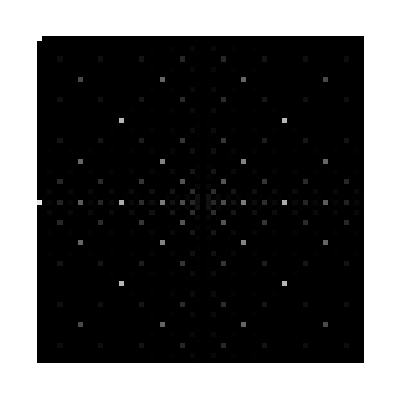

```mathematica
ArrayPlot[Log[0.01+Abs[RotateLeft[Fourier[bayer6-0.5],Dimensions[bayer6]/2]]],ColorFunction->GrayLevel]
```

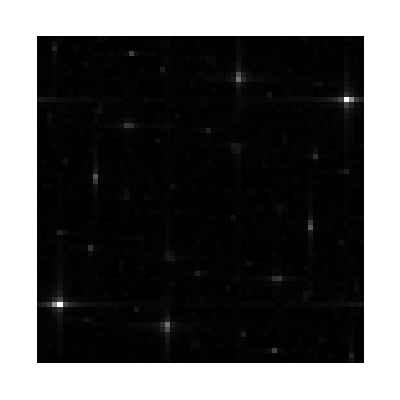

-Graphics3D-

```mathematica
MyTwoDimPeriodogram[Table[InterleavedGradientNoise[x,y],{y,0,63},{x,0,63}]-0.5]
ListPlot3D[Abs[RotateLeft[Fourier[Table[InterleavedGradientNoise[x,y],{y,0,63},{x,0,63}]-0.5],{32,32}]],PlotRange->{0,2},ColorFunction->"Rainbow"]
```

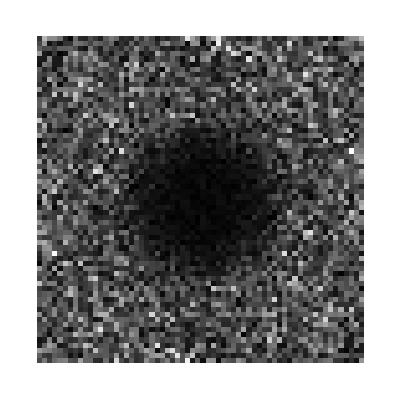

```mathematica
MyTwoDimPeriodogram[blueNoise64-0.5]
```

```mathematica
ListPlot3D[Abs[RotateLeft[Fourier[blueNoise64-0.5],Dimensions[bayer6]/2]],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListAnimate[{MyTwoDimPeriodogram[blueNoise64-0.5],MyTwoDimPeriodogram[Table[RandomReal[],{x,0,63},{y,0,63}]-0.5]}]
```

```mathematica
Export["2dwhitenoisevsbluenoise.gif",{MyTwoDimPeriodogram[blueNoise64-0.5],MyTwoDimPeriodogram[Table[RandomReal[],{x,0,63},{y,0,63}]-0.5]},"DisplayDurations"->2];
```

```mathematica
ListAnimate[{ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[ditheredBlue,ColorFunction->GrayLevel]}]
```

```mathematica
Export["2dwhitenoisevsbluenoise.gif",{ArrayPlot[ditheredWhite,ColorFunction->GrayLevel],ArrayPlot[ditheredBlue,ColorFunction->GrayLevel]},"DisplayDurations"->2];
```

```mathematica
GraphicsRow[{GaussianFilter[Image[ditheredWhite],2],GaussianFilter[Image[ditheredBlue],2]}]
```

-Graphics-

```mathematica
ListAnimate[{ArrayPlot[Map[QuantizeBits[#1,3,(RandomReal[]+RandomReal[]-1)]&,origSignal,{2}],ColorFunction->GrayLevel],ArrayPlot[MapIndexed[QuantizeBits[#1,3,remaptri[SampleArrayWithWrap[blueNoise64,#2[[1]],#2[[2]]]]]&,origSignal,{2}],ColorFunction->GrayLevel]}]
```

```mathematica
Export["2dwhitenoisevsbluenoisetriangle.gif",{ArrayPlot[Map[QuantizeBits[#1,3,(RandomReal[]+RandomReal[]-1)]&,origSignal,{2}],ColorFunction->GrayLevel],ArrayPlot[MapIndexed[QuantizeBits[#1,3,remaptri[SampleArrayWithWrap[blueNoise64,#2[[1]],#2[[2]]]]]&,origSignal,{2}],ColorFunction->GrayLevel]},"DisplayDurations"->2];
```

```mathematica
ditheredInterleavedRemap=MapIndexed[QuantizeBits[#1,3,remaptri[InterleavedGradientNoise[#2[[1]],#2[[2]]]]]&,origSignal,{2}];
```

```mathematica
ditheredBayerRemap=MapIndexed[QuantizeBits[#1,3,remaptri[SampleArrayWithWrap[bayer3,#2[[1]],#2[[2]]]]]&,origSignal,{2}];
ditheredWhiteRemap=Map[QuantizeBits[#1,3,remaptri[RandomReal[]]]&,origSignal,{2}];
```

```mathematica
ditheredBlueRemap=MapIndexed[QuantizeBits[#1,3,remaptri[SampleArrayWithWrap[blueNoise64,#2[[1]],#2[[2]]]]]&,origSignal,{2}];
```

```mathematica
GraphicsGrid[{{ArrayPlot[ditheredWhiteRemap,ColorFunction->GrayLevel],ArrayPlot[ditheredBlueRemap,ColorFunction->GrayLevel]},{ArrayPlot[ditheredBayerRemap,ColorFunction->GrayLevel],ArrayPlot[ditheredInterleavedRemap,ColorFunction->GrayLevel]}}]
```

-Graphics-

```mathematica
Export["2dditheringallfourcomparedtriangular.gif",{ArrayPlot[ditheredWhiteRemap,ColorFunction->GrayLevel],ArrayPlot[ditheredBlueRemap,ColorFunction->GrayLevel],ArrayPlot[ditheredBayerRemap,ColorFunction->GrayLevel],ArrayPlot[ditheredInterleavedRemap,ColorFunction->GrayLevel]},"DisplayDurations"->2];
```